## Fuel Cell

```mathematica
ucell:=Enernst-uact-uohmic-ucon
```

Nernst equation

```mathematica
Enernst:=dG/(2 F)+dS/(2 F)(T-Tref)+(R T)/(2 F)Log[(Ph2 √Po2)/P0]
```

```mathematica
uact=-(ksi1+ksi2 T + ksi3 T Log[Co2]+ksi4 T Log[iFC]);
```

```mathematica
uohmic=(rhoM l)/A
```

(0.7264 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)

```mathematica
rhoM=(181.6 (1+0.03(iFC/(A 10^4))+0.062(T/303)^2(iFC/(A 10^4))^2.5))/(psi-0.634-3(iFC/(A 10^4))E^(4.18((T-303)/T)))
```

(181.6 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)

```mathematica
uohmic
```

(0.7264 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)

```mathematica
Co2=Po2/(5.08 10^6 E^(-498/T))
```

1.92714×10^-7

```mathematica
ucon=-B Log[1-J/Jmax]
```

-0.15 Log[1-0.0238095 iFC]

```mathematica
LogA1m[x_]:=(x+x^2/2)/(1-(0.93x)^4)
```

```mathematica
LogA1m[x_]:=(1.3 x)/(1-(0.93x)^4)
```

```mathematica
ucon=B LogA1m[J/Jmax]
```

(0.00464286 iFC)/(1-2.404×10^-7 iFC^4)

## Conductances

```mathematica
conA=Simplify[iFC/Simplify[Together[(uact+ucon)]]]
```

(iFC (-4.15973×10^6+1. iFC^4))/(-489487.-19313. iFC+0.117673 iFC^4+(-142622.+0.0342865 iFC^4) Log[iFC])

```mathematica
conOhm=iFC/(uohmic)
```

(1.37665 (22.366-0.0621794 iFC) iFC)/(1+0.00048 iFC+2.28145×10^-6 iFC^2.5)

```mathematica
Enernst
```

1.19719

```mathematica
ksi2:=0.00286+0.0002 Log[A 10^4]+4.3 10^-5 Log[Ch2]
```

```mathematica
dS=.85 10^-3 2F
```

164.025

```mathematica
psi=23.;T=300;
```

```mathematica
F=96485.33212;
R=8.314;
Tref=298.15;
dG=228000.6;
P0=1;
```

```mathematica
n=48;
T=323;
A=62.5 10^-4;
l=25 10^-6;
Ph2=1.476;
Po2=0.2095;
B=0.15;
Rc=0.0003;ksi1=-.948;ksi3=7.22 10^-5;ksi4=-1.0615 10^-4;
psi=23;
Jmax=672 10^-3 10^4;
Jn=22 10^-3 10^4;
Imax=42;
```

```mathematica
J=iFC/A
```

160. iFC

```mathematica
ksi2:=0.00286+0.0002 Log[A 10^4]+4.3 10^-5 Log[Ch2]
```

```mathematica
Ch2=1;
```

```mathematica
ucell
```

1.07952-(0.7264 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)-(0.00464286 iFC)/(1-2.404×10^-7 iFC^4)-0.0342865 Log[iFC]

```mathematica
Enernst
```

1.19719

```mathematica
conA=iFC/(uact+ucon)
```

iFC/(0.117673+(0.00464286 iFC)/(1-2.404×10^-7 iFC^4)+0.0342865 Log[iFC])

```mathematica
rhoM
```

(181.6 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)

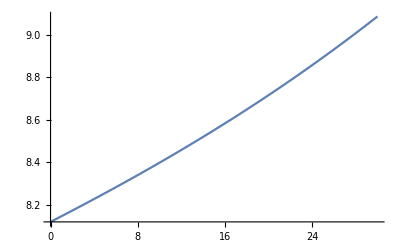

```mathematica
Plot[rhoM,{iFC,0,30}]
```

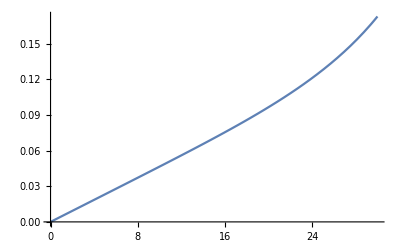

```mathematica
Plot[ucon,{iFC,0,30}]
```

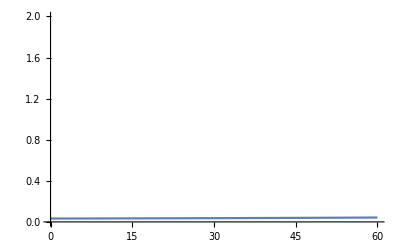

```mathematica
Plot[uohmic,{iFC,0,60},PlotRange->{0,2}]
```

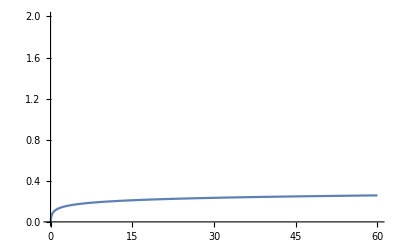

```mathematica
Plot[uact,{iFC,0,60},PlotRange->{0,2}]
```

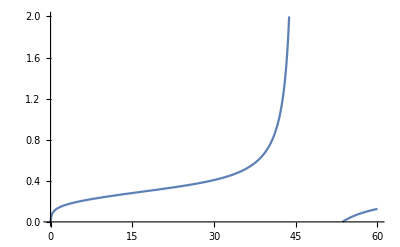

```mathematica
Plot[{uact+ucon},{iFC,0,60},PlotRange->{0,2}]
```

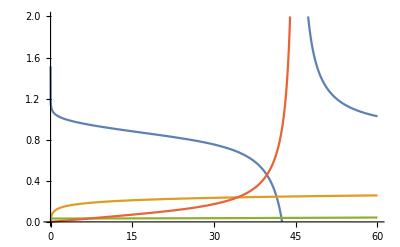

```mathematica
Plot[{ucell,uact,uohmic,ucon},{iFC,0,60}, PlotRange->{0,2}]
```

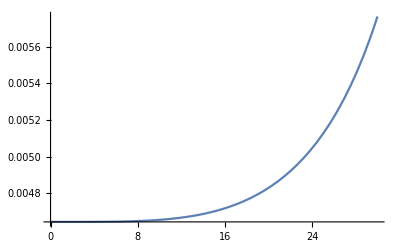

```mathematica
Plot[ucon/iFC,{iFC,0,30}]
```

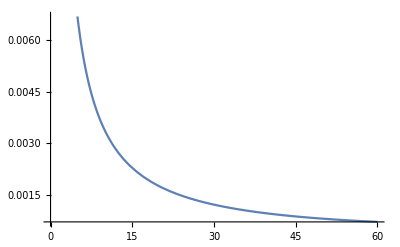

```mathematica
Plot[uohmic/iFC,{iFC,0,60}]
```

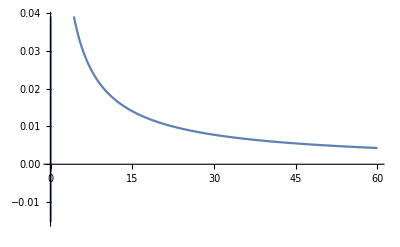

```mathematica
Plot[uact/iFC,{iFC,0,60}]
```

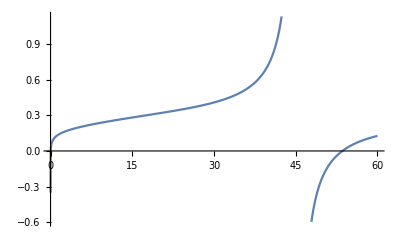

```mathematica
Plot[{uact+ucon},{iFC,0,60}]
```

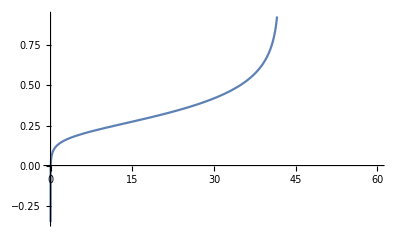

-Graphics-

```mathematica
Nernst
```

Nernst

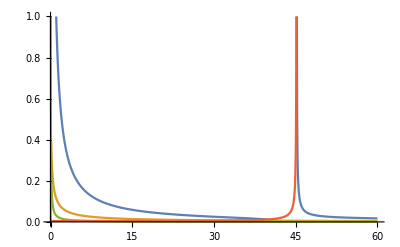

```mathematica
Plot[{ucell/iFC,uact/iFC,uohmic/iFC,ucon/iFC},{iFC,0,60}, PlotRange->{0,01}]
```

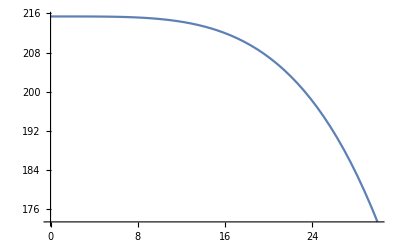

```mathematica
Plot[iFC/ucon,{iFC,0,30}]
```

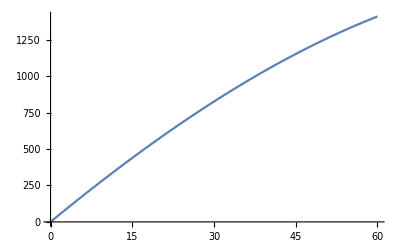

```mathematica
Plot[iFC/uohmic,{iFC,0,60}]
```

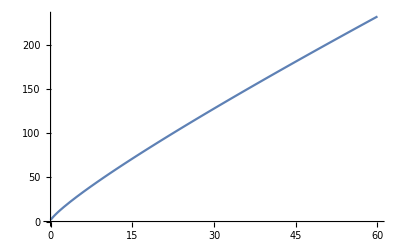

```mathematica
Plot[iFC/uact,{iFC,0,60}]
```

```mathematica
1/0.02380952380952381
```

42.

```mathematica
conA=iFC/(uact+ucon)
```

iFC/(0.117673+(0.00464286 iFC)/(1-2.404×10^-7 iFC^4)+0.0342865 Log[iFC])

```mathematica
Series[(x1+x1^2/2)/(1-x^4),{x1,0,3}]
```

x1/(1-x^4)-x1^2/(2 (-1+x^4))+O[x1]^4

```mathematica
Series[x/(-Log[1-x]),{x,.7,4}]
```

0.581408-0.779111 (x-0.7)-0.525768 (x-0.7)^2-0.91109 (x-0.7)^3-1.96695 (x-0.7)^4+O[x-0.7]^5

```mathematica
x=.;
```

```mathematica
Series[(x+x^2/2+x^3/3)/(-Log[1-x]),{x,.7,3}]
```

0.879865-0.617026 (x-0.7)-1.355 (x-0.7)^2-2.14673 (x-0.7)^3+O[x-0.7]^4

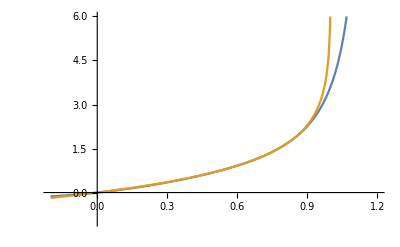

```mathematica
Plot[{(x)/(0.5814084815577761-0.7791108474285051 (x-0.7)-0.525768488620312 (x-0.7)^2-0.9110897346409232 (x-0.7)^3),-Log[1-x]},{x,-.2,1.2},PlotRange->{-1,6}]
```

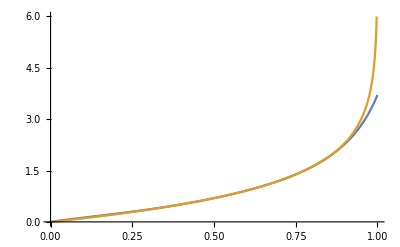

```mathematica
Plot[{(x+x^2/2+x^3/3)/(0.8990-0.5333 (x-0.6667)-1.164 (x-0.6667)^2-1.6980 (x-0.6667)^3-2.797 (x-0.6667)^4),-Log[1-x]},{x,0,1},PlotRange->{0,6}]
```

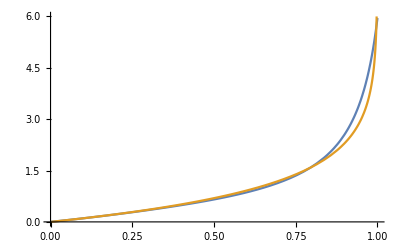

```mathematica
Plot[{(x+x^2/2)/(1-(0.93x)^4),-Log[1-x]},{x,0,1},PlotRange->{0,6}]
```

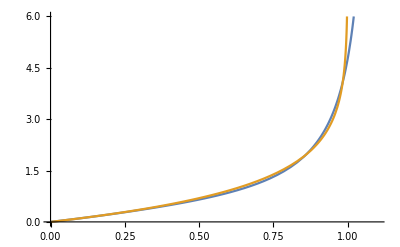

```mathematica
Plot[{(x+x^2/2)/(1-(0.91x)^4),-Log[1-x]},{x,0,1.1},PlotRange->{0,6}]
```

```mathematica
Plot[{(1.3 x)/(1-(0.93x)^4),-Log[1-x]},{x,0,1},PlotRange->{0,4}]
```

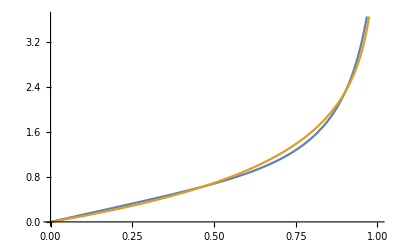

```mathematica
Plot[{(1.3 x)/(1-(0.93x)^4),-Log[1-x]},{x,0,1}]
```

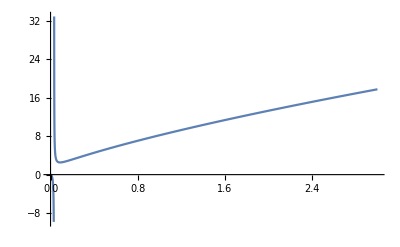

```mathematica
Plot[{conA},{iFC,0,3}]
```

```mathematica
x
```

x

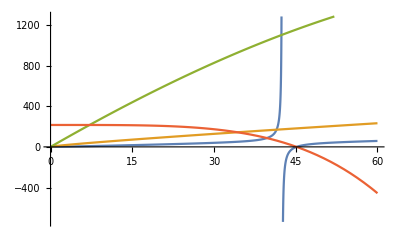

```mathematica
Plot[{iFC/ucell,iFC/uact,iFC/uohmic,iFC/ucon},{iFC,0,60}]
```

```mathematica
422./834
```

0.505995

```mathematica
2*200./8140
```

0.04914